# Computational Essay

## Machine Learning

```mathematica
(-Graphics-)_□
```

## Resource Objects

```mathematica
ResourceObject["Sample Data: Birth Weight Risk"]
```

ResourceObject[…]

#### Wolfram Data Repository

https://datarepository.wolframcloud.com

### Fetching Data

```mathematica
df = ResourceData["Sample Data: Birth Weight Risk"];
```

## Question

Dataset Format

```mathematica
df[1,All]
```

Dataset[<>]

How many 18 years old’s smoke ?

```mathematica
df[Select[#Age==Quantity[18,"Years"]&& TrueQ[#Smoker]&],All]
```

Dataset[<>]

How many X year’s old’s smoke ?

```mathematica
Manipulate[
Grid[{
{"Size of the dataset is "<>ToString@Length[df[Select[#Age==Quantity[n,"Years"]&& TrueQ[#Smoker]&],All]]},
{df[Select[#Age==Quantity[n,"Years"]&& TrueQ[#Smoker]&],All]}
}],
{{n,18,"Age"},14,45,1}]
```

I have many questions

```mathematica
Manipulate[
df[Select[#Age==Quantity[n,"Years"]&& #Smoker==a && #Hypertension==b&],All],
{{n,18,"Age"},QuantityMagnitude@Min[df[All,"Age"]],QuantityMagnitude@Max[df[All,"Age"]],1},
{{a,False,"Smoker?"},{True,False}},
{{b,False,"Hypertension?"},{True,False}}
]
```

What is the age distribution ?

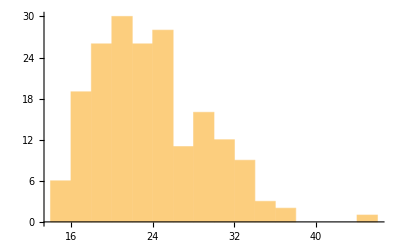

```mathematica
Histogram[df[All,"Age"]]
```

What is the X distribution ?

```mathematica
Manipulate[Histogram[df[All,X],bins,var],
{{X,"Age","Feature"},{"Age","LWT","BWT"}},
{{bins,Automatic,"bins"},5,45,5},
{{var,Automatic,"operation"},{"PDF","Probability","CumulativeCount"}}]
```

LWT vs BWT

```mathematica
Manipulate[ListPlot[df[All,{"Age",x}]],{x,{"LWT","BWT"}}]
```

ListPlot::lpn: df[All,{Age,LWT}] is not a list of numbers or pairs of numbers.

## Wrangle

```mathematica
mySample = df[Select[#Age ≥ Quantity[20,"Years"] && #Age < Quantity[30,"Years"]&],All];
```

```mathematica
uniqueAge = DeleteDuplicates[df[All,"Age"]];
```

```mathematica
Normal[uniqueAge]
```

{19 yr,33 yr,20 yr,21 yr,18 yr,22 yr,17 yr,29 yr,26 yr,30 yr,15 yr,25 yr,28 yr,32 yr,31 yr,36 yr,24 yr,35 yr,27 yr,23 yr,16 yr,14 yr,45 yr,34 yr}

Valid Features

```mathematica
features = {"Low","Age","LWT","Hypertension","UI","BWT"};
```

Smoker and Non-Smokers

```mathematica
smoker = Normal[df[Select[TrueQ[#Smoker]&],features]];
```

```mathematica
nonSmoker = Normal[df[Select[!TrueQ[#Smoker]&],features]];
```

### Classify

#### Classes and Labels

```mathematica
prepSmoker =smoker⟦#⟧->"smoker"&/@Range[Length[smoker]] ;
```

```mathematica
prepNonSmoker = nonSmoker⟦#⟧->"nonSmoker"&/@Range[Length[nonSmoker]];
```

```mathematica
fullData = Flatten[{prepNonSmoker,prepSmoker}];
```

```mathematica
fullData⟦1⟧
```

<|Low→False,Age→19 yr,LWT→182 lb,Hypertension→False,UI→True,BWT→2523 g|>→nonSmoker

#### Build Model

```mathematica
c = Classify[fullData,TargetDevice->"CPU",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Mixed (number: 6)
Classes | ,,nonSmokersmoker
Accuracy | (62.7.) %
Method | NearestNeighbors
Single evaluation time | 3.14 ms/example
Batch evaluation speed | 41.4 examples/ms
Loss | 0.666 ± 0.03
Model memory | 314. kB
Training examples used | 189 examples
Training time | 3.54 s
 |

#### Test Model

```mathematica
query = <|
"Low" -> False,
"Age"->Quantity[33,"Years"],
"LWT"->Quantity[130,"Pounds"],
"Hypertension"->True, 
"UI"-> False, 
"BWT"->Quantity[233,"Grams"]
|>
```

<|Low→False,Age→33 yr,LWT→130 lb,Hypertension→True,UI→False,BWT→233 g|>

```mathematica
PieChart[c[query,"Probabilities"],ChartLabels->Automatic]
```

-Graphics-

```mathematica
c[query,"TopProbabilities"]
```

{nonSmoker→0.520865,smoker→0.479135}

## Explore

Unique Ages and their features.

```mathematica
collection = Table[QuantityMagnitude[uniqueAge⟦i⟧]->df[Select[#Age == uniqueAge⟦i⟧&],All],{i,Length[uniqueAge]}];
```

```mathematica
cluster = FindClusters[collection];
```

```mathematica
FeatureSpacePlot3D[Transpose[cluster],LabelingFunction->Callout]
```

-Graphics3D-

## Analyze

#### Prepare Data

```mathematica
prep = Table[Normal[Normal[df[i,All]]]-> DeleteDuplicates[Normal[Normal[df[i,All]]["Age"]]],{i,Length[df]}];
```

```mathematica
data = Table[Normal[KeyDrop[Association[First[prep⟦i⟧]],{"Age","MotherID","FTV","Race","PTL"}]]-> DeleteDuplicates[Normal[Normal[df[i,All]]["Age"]]],{i,Length[df]}];
```

#### Machine Learning Model Version 1

```mathematica
data⟦1⟧
```

{Low→False,LWT→182 lb,Smoker→False,Hypertension→False,UI→True,BWT→2523 g}→19 yr

```mathematica
model = Predict[data]
```

PredictorFunction[…]

#### Machine Learning Model Version 2

```mathematica
modelv2 = Predict[data,Method->"DecisionTree",TargetDevice->"CPU",PerformanceGoal->"Speed"]
```

PredictorFunction[…]

#### Test Machine Learning Algorithms

```mathematica
Manipulate[
Information[Predict[data,Method->x,PerformanceGoal->"Speed"]],
{{x,"LinearRegression","Algorithm"},{
"DecisionTree",
"LinearRegression",
"GradientBoostedTrees",
"NearestNeighbors",
"NeuralNetwork",
"Random Forest",
"GaussianProcess"}}]
```

Predict::bdfmt: Argument data should be a rule or a list of rules.

```mathematica
query = {
"Low"->True,
"LWT"->Quantity[182, "Pounds"],
"Smoker"->False,
"Hypertension"->False,
"UI"->False,
"BWT"->Quantity[2523, "Grams"]
};
```

```mathematica
model[query]
```

22.9046 yr

```mathematica
modelv2[query]
```

19. yr

```mathematica
Information[model]
```

Predictor information
Data type | Mixed (number: 6)
Standard deviation | 1.67×10^8 ± 1.2×10^7
Method | LinearRegression
Single evaluation time | 2.6 ms/example
Batch evaluation speed | 10.2 examples/ms
Loss | 20.4 ± 0.062
Model memory | 320. kB
Training examples used | 189 examples
Training time | 1.8 s
 |

## Communicate

#### Automating API Construction

```mathematica
f = Drop[Keys[Association[query]]];
```

```mathematica
restFormat = ToLowerCase[#]&/@f;
```

```mathematica
returnTypes = {"Boolean","Integer","Integer","Boolean","Integer","Boolean","Boolean","Integer","Integer"};
```

```mathematica
restTemplate = Thread[restFormat->returnTypes];
```

#### API Version 1 (Linear Regression)

```mathematica
v1 = APIFunction[{
"low"->"Boolean",
"lwt"->"Integer",
"smoker"->"Boolean",
"hypertension"->"Boolean",
"ui"->"Boolean",
"bwt"->"Integer"
},(
ExportString[
Association[
"guess"->
QuantityMagnitude[model[
{
"low"->#low,
"lwt"->Quantity[#lwt,"Pounds"],
"smoker"->#smoker,
"hypertension"-> #hypertension,
"ui"-> #ui,
"bwt"-> Quantity[#bwt,"Grams"]
}
]]],"JSON"]&)
];
```

#### API Version 2 (Decision Tree)

```mathematica
v2 = APIFunction[{
"low"->"Boolean",
"lwt"->"Integer",
"smoker"->"Boolean",
"ptl"->"Integer",
"hypertension"->"Boolean",
"ui"->"Boolean",
"bwt"->"Integer"
},(
ExportString[
Association[
"guess"->
QuantityMagnitude[modelv2[
{
"low"->#low,
"lwt"->Quantity[#lwt,"Pounds"],
"smoker"->#smoker,
"hypertension"-> #hypertension,
"ui"-> #ui,
"bwt"-> Quantity[#bwt,"Grams"]
}
]]],"JSON"]&)
];
```

#### Testing API

```mathematica
testQuery = {"low"->False,"lwt"->100,"smoker"->True,"hypertension"->False,"ui"->True,"bwt"->200};
```

```mathematica
v1[testQuery]
```

{
	"guess":2.3904923232699428e1
}

```mathematica
v2[testQuery]
```

{
	"guess":1.9000000105739893e1
}

#### URL

```mathematica
private = #<>"?low=True&lwt=100&smoker=True&hypertension=True&ui=True&bwt=200"&;
```

#### Publish to Cloud

```mathematica
(*CloudPublish[_,Permissions->"Public"]*)
```

CloudObject[https://www.wolframcloud.com/obj/99377e14-3c78-4e4a-a074-426f5ec4882a]

## Miscellaneous

```mathematica
ResourceObject["CIFAR-10"]
```

ResourceObject[…]

```mathematica
(*allData = RandomSample[ResourceData["CIFAR-10"],1000];*)
```

```mathematica
DeleteDuplicates[Last[allData⟦#⟧]&/@Range[Length[allData]]]
```

{deer,frog,airplane,cat,ship,bird,truck,dog,automobile,horse}

```mathematica
myRestrictions = {"cat","dog","horse","deer","frog","bird"};
```

```mathematica
g[x_]:=Select[allData,Last[#]==x&];
```

```mathematica
readyData = Flatten[g[#]&/@myRestrictions];
```

```mathematica
readyData//Length
```

601

### Splitting data

```mathematica
(Length[readyData] * 80) / 100 //N
```

480.8

```mathematica
trainingData = RandomChoice[readyData,481];
```

```mathematica
testData = RandomChoice[readyData,200];
```

```mathematica
validation = trainingData ∩ testData;
```

## Classify

```mathematica
c = Classify[trainingData]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Image
Number of classes | 6
Accuracy | (89.32.8) %
Method | LogisticRegression
Single evaluation time | 147. ms/example
Batch evaluation speed | 5.18 examples/s
Loss | 0.418 ± 0.086
Model memory | 310. kB
Training examples used | 481 examples
Training time | 1 17
 |

#### Testing Images

```mathematica
testModel = -Graphics-;
```

```mathematica
testCat = -Graphics-;
```

```mathematica
testBird = First[trainingData[[55]]]
```

-Graphics-

#### Testing Model

```mathematica
c[testModel]
```

dog

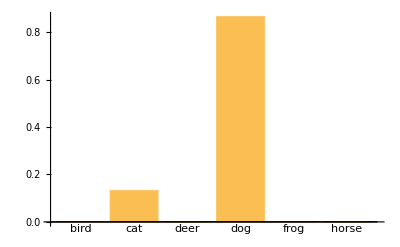

```mathematica
BarChart[c[testCat,"Probabilities"],ChartLabels->Automatic]
```

```mathematica
c[testCat,"TopProbabilities"]
```

{dog→0.865751,cat→0.132795}

```mathematica
c[testBird]
```

bird

#### A Cool App

## Measurements

```mathematica
measurements = ClassifierMeasurements[c,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
Manipulate[measurements[x],{x,measurements["Properties"]}]
```